## Here we check summation by parts for the Full and Sparse Hierarchical bases in 2D.

### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=If[l==-1,1,If[l==0,#,ϕ[2^l(#-2^-l(2i-1))]]]&
ϕ[lx_,ly_,i_,j_]:=ϕ[lx,i][#1]ϕ[ly,j][#2]&
ψ[lx_,ly_,i_,j_]:=ϕ[2^lx(#1-2^-lx i)]ϕ[2^ly(#2-2^-ly j)]&
ceil[x_,l_]:=If[x≥1,2^(l-1),1+Floor[2^(l-1)x]]
switch[x_]:=If[x≥1,x,1]
dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]](* Don't think I need this*)
```

### Standard Basis

```mathematica
standardCoefficients2D[f_,lx_,ly_]:=Table[f[2^-lx i,2^-ly j],{i,0,2^lx},{j,0,2^ly}]
standardReconstruct2D[coefficients_,lx_,ly_]:=Sum[coefficients[[i+1,j+1]] ψ[lx,ly,i,j][#1,#2],{i,0,2^lx},{j,0,2^ly}]&

standardProject2D[f_,lx_,ly_]:=standardReconstruct2D[standardCoefficients2D[f,lx,ly],lx,ly]
```

### Full Basis

```mathematica
getCoefficient[f_,x_,l_]:=If[l==-1,f[0],If[l==0,f[1]-f[0],f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]]]

getCoefficient2D[f_,x_,y_,lx_,ly_]:=getCoefficient[Function[y1,getCoefficient[Function[x1,f[x1,y1]],x,lx]],y,ly]
(* Tensor product construction
*)

fullCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^switch[kx]-1,2},{j,1,2^switch[ky]-1,2}],{kx,-1,lx},{ky,-1,ly}]


Reconstruct2D[coefficients_]:= Sum[coefficients[[kx+2,ky+2,ceil[#1,switch[kx]],ceil[#2,switch[ky]]]] 
ϕ[kx,ky,ceil[#1,switch[kx]],ceil[#2,switch[ky]]][#1,#2]
,{kx,-1,Length[coefficients]-2},{ky,-1,Length[coefficients]-2}]&

reverseFlatten[coefficients_,kx_,ky_]:=Module[{k},k=0;Return[Table[Table[coefficients[[++k]] ,{i,1,2^(switch[lx]-1)},{j,1,2^(switch[ly]-1)}],{lx,-1,kx},{ly,-1,ky}]];]


project2D[f_,lx_,ly_]:=Reconstruct2D[fullCoefficients2D[f,lx,ly]]
```

### Sparse Basis

```mathematica
sparseCoefficients2D[f_,n_]:=Table[Table[Table[getCoefficient2D[f,2^-row i,2^(-(diag-row-1)) j,row,(diag-row-1)],{i,1,2^switch[row]-1,2},{j,1,2^switch[diag-row-1]-1,2}],{row,-1,diag}],{diag,-1,n}]

sparseReconstruct[coefficients_]:=Sum[Sum[coefficients[[diag+2,row+2,ceil[#1,switch[row]],ceil[#2,switch[diag-row-1]]]] 
ϕ[row,diag-row-1,ceil[#1,switch[row]],ceil[#2,switch[diag-row-1]]][#1,#2]
,{row,-1,diag}],{diag,-1,Length[coefficients]-2}]&

sparseProject[f_,n_]:=sparseReconstruct[sparseCoefficients2D[f,n]]
```

```mathematica
fullW[lx_,ly_]:=Table[Table[Table[Table[NIntegrate[ϕ[kx1,ky1,i1,j1][x,y] ϕ[kx2,ky2,i2,j2][x,y],{x,0,1},{y,0,1}],{i2,1,2^(switch[kx2]-1)},{j2,1,2^(switch[ky2]-1)}],{kx2,-1,lx},{ky2,-1,ly}]//Flatten,{i1,1,2^(switch[kx1]-1)},{j1,1,2^(switch[ky1]-1)}],{kx1,-1,lx},{ky1,-1,ly}]
```

```mathematica
fullW[2,2]
```

{{{{{1.,0.5,0.5,0.25,0.25,0.5,0.25,0.25,0.125,0.125,0.5,0.25,0.25,0.125,0.125,0.25,0.25,0.125,0.125,0.125,0.125,0.0625,0.0625,0.0625,0.0625}}},{{{0.5,0.333333,0.25,0.0625,0.1875,0.25,0.166667,0.125,0.03125,0.09375,0.25,0.166667,0.125,0.03125,0.09375,0.125,0.125,0.0833333,0.0833333,0.0625,0.0625,0.015625,0.046875,0.015625,0.046875}}},{{{0.5,0.25,0.333333,0.125,0.125,0.25,0.125,0.166667,0.0625,0.0625,0.25,0.125,0.166667,0.0625,0.0625,0.125,0.125,0.0625,0.0625,0.0833333,0.0833333,0.03125,0.03125,0.03125,0.03125}}},{{{0.25,0.0625,0.125,0.166667,0.,0.125,0.03125,0.0625,0.0833333,0.,0.125,0.03125,0.0625,0.0833333,0.,0.0625,0.0625,0.015625,0.015625,0.03125,0.03125,0.0416667,0.,0.0416667,0.},{0.25,0.1875,0.125,0.,0.166667,0.125,0.09375,0.0625,0.,0.0833333,0.125,0.09375,0.0625,0.,0.0833333,0.0625,0.0625,0.046875,0.046875,0.03125,0.03125,0.,0.0416667,0.,0.0416667}}}},{{{{0.5,0.25,0.25,0.125,0.125,0.333333,0.166667,0.166667,0.0833333,0.0833333,0.25,0.125,0.125,0.0625,0.0625,0.0625,0.1875,0.03125,0.09375,0.03125,0.09375,0.015625,0.015625,0.046875,0.046875}}},{{{0.25,0.166667,0.125,0.03125,0.09375,0.166667,0.111111,0.0833333,0.0208333,0.0625,0.125,0.0833333,0.0625,0.015625,0.046875,0.03125,0.09375,0.0208333,0.0625,0.015625,0.046875,0.00390625,0.0117187,0.0117187,0.0351563}}},{{{0.25,0.125,0.166667,0.0625,0.0625,0.166667,0.0833333,0.111111,0.0416667,0.0416667,0.125,0.0625,0.0833333,0.03125,0.03125,0.03125,0.09375,0.015625,0.046875,0.0208333,0.0625,0.0078125,0.0078125,0.0234375,0.0234375}}},{{{0.125,0.03125,0.0625,0.0833333,0.,0.0833333,0.0208333,0.0416667,0.0555556,0.,0.0625,0.015625,0.03125,0.0416667,0.,0.015625,0.046875,0.00390625,0.0117187,0.0078125,0.0234375,0.0104167,0.,0.03125,0.},{0.125,0.09375,0.0625,0.,0.0833333,0.0833333,0.0625,0.0416667,0.,0.0555556,0.0625,0.046875,0.03125,0.,0.0416667,0.015625,0.046875,0.0117187,0.0351563,0.0078125,0.0234375,0.,0.0104167,0.,0.03125}}}},{{{{0.5,0.25,0.25,0.125,0.125,0.25,0.125,0.125,0.0625,0.0625,0.333333,0.166667,0.166667,0.0833333,0.0833333,0.125,0.125,0.0625,0.0625,0.0625,0.0625,0.03125,0.03125,0.03125,0.03125}}},{{{0.25,0.166667,0.125,0.03125,0.09375,0.125,0.0833333,0.0625,0.015625,0.046875,0.166667,0.111111,0.0833333,0.0208333,0.0625,0.0625,0.0625,0.0416667,0.0416667,0.03125,0.03125,0.0078125,0.0234375,0.0078125,0.0234375}}},{{{0.25,0.125,0.166667,0.0625,0.0625,0.125,0.0625,0.0833333,0.03125,0.03125,0.166667,0.0833333,0.111111,0.0416667,0.0416667,0.0625,0.0625,0.03125,0.03125,0.0416667,0.0416667,0.015625,0.015625,0.015625,0.015625}}},{{{0.125,0.03125,0.0625,0.0833333,0.,0.0625,0.015625,0.03125,0.0416667,0.,0.0833333,0.0208333,0.0416667,0.0555556,0.,0.03125,0.03125,0.0078125,0.0078125,0.015625,0.015625,0.0208333,0.,0.0208333,0.},{0.125,0.09375,0.0625,0.,0.0833333,0.0625,0.046875,0.03125,0.,0.0416667,0.0833333,0.0625,0.0416667,0.,0.0555556,0.03125,0.03125,0.0234375,0.0234375,0.015625,0.015625,0.,0.0208333,0.,0.0208333}}}},{{{{0.25,0.125,0.125,0.0625,0.0625,0.0625,0.03125,0.03125,0.015625,0.015625,0.125,0.0625,0.0625,0.03125,0.03125,0.166667,0.,0.0833333,0.,0.0833333,0.,0.0416667,0.0416667,0.,0.}},{{0.25,0.125,0.125,0.0625,0.0625,0.1875,0.09375,0.09375,0.046875,0.046875,0.125,0.0625,0.0625,0.03125,0.03125,0.,0.166667,0.,0.0833333,0.,0.0833333,0.,0.,0.0416667,0.0416667}}},{{{0.125,0.0833333,0.0625,0.015625,0.046875,0.03125,0.0208333,0.015625,0.00390625,0.0117187,0.0625,0.0416667,0.03125,0.0078125,0.0234375,0.0833333,0.,0.0555556,0.,0.0416667,0.,0.0104167,0.03125,0.,0.}},{{0.125,0.0833333,0.0625,0.015625,0.046875,0.09375,0.0625,0.046875,0.0117187,0.0351563,0.0625,0.0416667,0.03125,0.0078125,0.0234375,0.,0.0833333,0.,0.0555556,0.,0.0416667,0.,0.,0.0104167,0.03125}}},{{{0.125,0.0625,0.0833333,0.03125,0.03125,0.03125,0.015625,0.0208333,0.0078125,0.0078125,0.0625,0.03125,0.0416667,0.015625,0.015625,0.0833333,0.,0.0416667,0.,0.0555556,0.,0.0208333,0.0208333,0.,0.}},{{0.125,0.0625,0.0833333,0.03125,0.03125,0.09375,0.046875,0.0625,0.0234375,0.0234375,0.0625,0.03125,0.0416667,0.015625,0.015625,0.,0.0833333,0.,0.0416667,0.,0.0555556,0.,0.,0.0208333,0.0208333}}},{{{0.0625,0.015625,0.03125,0.0416667,0.,0.015625,0.00390625,0.0078125,0.0104167,0.,0.03125,0.0078125,0.015625,0.0208333,0.,0.0416667,0.,0.0104167,0.,0.0208333,0.,0.0277778,0.,0.,0.},{0.0625,0.046875,0.03125,0.,0.0416667,0.015625,0.0117187,0.0078125,0.,0.0104167,0.03125,0.0234375,0.015625,0.,0.0208333,0.0416667,0.,0.03125,0.,0.0208333,0.,0.,0.0277778,0.,0.}},{{0.0625,0.015625,0.03125,0.0416667,0.,0.046875,0.0117187,0.0234375,0.03125,0.,0.03125,0.0078125,0.015625,0.0208333,0.,0.,0.0416667,0.,0.0104167,0.,0.0208333,0.,0.,0.0277778,0.},{0.0625,0.046875,0.03125,0.,0.0416667,0.046875,0.0351563,0.0234375,0.,0.03125,0.03125,0.0234375,0.015625,0.,0.0208333,0.,0.0416667,0.,0.03125,0.,0.0208333,0.,0.,0.,0.0277778}}}}}

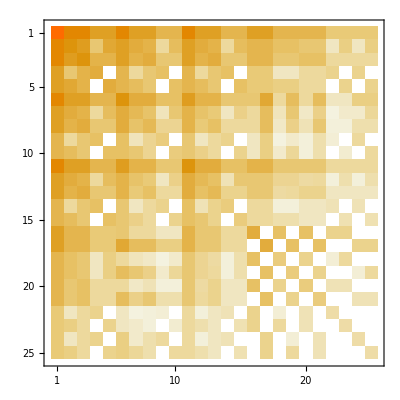

```mathematica
Flatten[Out[286],3]//MatrixPlot
```

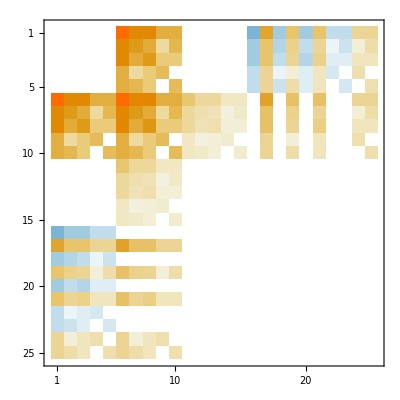

```mathematica
SetAccuracy[(#+Transpose[#])&@(Flatten[dxMatrix[2,2],3].Flatten[Out[286],3]),3]//MatrixPlot
```

I think this is actually what we’re looking for... only boundary terms contribute. The interior is zero.

```mathematica
fulldW[lx_,ly_]:=Table[Table[Table[Table[NIntegrate[ϕ[kx1,ky1,i1,j1][1,y] ϕ[kx2,ky2,i2,j2][1,y],{y,0,1}]-NIntegrate[ϕ[kx1,ky1,i1,j1][0,y] ϕ[kx2,ky2,i2,j2][0,y],{y,0,1}]-NIntegrate[ϕ[kx1,ky1,i1,j1][x,1] ϕ[kx2,ky2,i2,j2][x,1],{x,0,1}]+NIntegrate[ϕ[kx1,ky1,i1,j1][x,0] ϕ[kx2,ky2,i2,j2][x,0],{x,0,1}],{i2,1,2^(switch[kx2]-1)},{j2,1,2^(switch[ky2]-1)}],{kx2,-1,lx},{ky2,-1,ly}]//Flatten,{i1,1,2^(switch[kx1]-1)},{j1,1,2^(switch[ky1]-1)}],{kx1,-1,lx},{ky1,-1,ly}]
```

```mathematica
fulldW[2,2]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{{{{0.,-1.,0.,0.,0.,1.,0.,0.5,0.25,0.25,0.,-0.5,0.,0.,0.,0.,0.,-0.25,-0.25,0.,0.,0.,0.,0.,0.}}},{{{-1.,-1.,0.,0.,0.,0.,-0.166667,0.25,0.0625,0.1875,-0.5,-0.5,0.,0.,0.,-0.25,-0.25,-0.25,-0.25,0.,0.,0.,0.,0.,0.}}},{{{0.,0.,0.,0.,0.,0.5,0.25,0.333333,0.125,0.125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}},{{{0.,0.,0.,0.,0.,0.25,0.0625,0.125,0.166667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,0.1875,0.125,0.,0.166667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}},{{{{1.,0.,0.5,0.25,0.25,1.,0.166667,0.5,0.25,0.25,0.,-0.25,0.,0.,0.,0.,0.,-0.0625,-0.1875,0.,0.,0.,0.,0.,0.}}},{{{0.,-0.166667,0.25,0.0625,0.1875,0.166667,0.,0.25,0.0625,0.1875,-0.25,-0.25,0.,0.,0.,-0.0625,-0.1875,-0.0625,-0.1875,0.,0.,0.,0.,0.,0.}}},{{{0.5,0.25,0.333333,0.125,0.125,0.5,0.25,0.333333,0.125,0.125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}},{{{0.25,0.0625,0.125,0.166667,0.,0.25,0.0625,0.125,0.166667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.25,0.1875,0.125,0.,0.166667,0.25,0.1875,0.125,0.,0.166667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}},{{{{0.,-0.5,0.,0.,0.,0.,-0.25,0.,0.,0.,0.,-0.333333,0.,0.,0.,0.,0.,-0.125,-0.125,0.,0.,0.,0.,0.,0.}}},{{{-0.5,-0.5,0.,0.,0.,-0.25,-0.25,0.,0.,0.,-0.333333,-0.333333,0.,0.,0.,-0.125,-0.125,-0.125,-0.125,0.,0.,0.,0.,0.,0.}}},{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}},{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}},{{{{0.,-0.25,0.,0.,0.,0.,-0.0625,0.,0.,0.,0.,-0.125,0.,0.,0.,0.,0.,-0.166667,0.,0.,0.,0.,0.,0.,0.}},{{0.,-0.25,0.,0.,0.,0.,-0.1875,0.,0.,0.,0.,-0.125,0.,0.,0.,0.,0.,0.,-0.166667,0.,0.,0.,0.,0.,0.}}},{{{-0.25,-0.25,0.,0.,0.,-0.0625,-0.0625,0.,0.,0.,-0.125,-0.125,0.,0.,0.,-0.166667,0.,-0.166667,0.,0.,0.,0.,0.,0.,0.}},{{-0.25,-0.25,0.,0.,0.,-0.1875,-0.1875,0.,0.,0.,-0.125,-0.125,0.,0.,0.,0.,-0.166667,0.,-0.166667,0.,0.,0.,0.,0.,0.}}},{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}},{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}}}

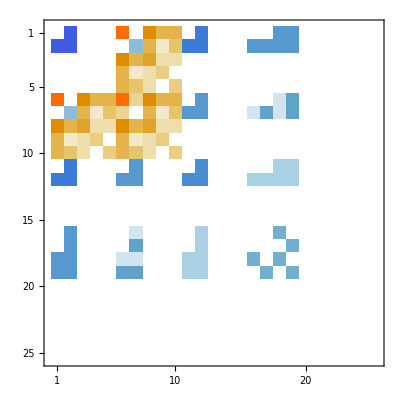

```mathematica
Flatten[Out[321],3]//MatrixPlot
```